# UV Hygrometer WECAN

## 2019-01-07

Fit UV Hygrometer signal to reference mixing ratio measurements (Aerodyne or Picarro).

Aerodyne used as H2O mixing ratio truth for most flights. Picarro2401 is two-second data rate.
Using data from Teresa’s R0 submission to the archive (after her calibration).

Using ATH1 for ambient temperature.

## Initialization

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
 AppendTo[$Path,"~/bin/MathematicaPackages/"];
SetDirectory[NotebookDirectory[]];
<<MurphyKoop`
```

```mathematica
kB=QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]]];
```

```mathematica
(* Data file names: 1 Hz netcdf, exported calculated mixing ratio (ppmv), and calibrated Aerodyne/Picarro file for water vapor reference. *)
datafile="/Users/Shared/BigStuff/WecanData/WECANrf01.nc";
exportFile="rf01.txt";
dataFileH2OReference="/Users/Shared/BigStuff/WecanData/AerodyneData_R0_2018-11-06/WECAN-CON2O_C130_20180724_R0.ict";
```

```mathematica
(* Cut off first 1000-2000 seconds after takeoff. Seems to take a while before the UVhygrometer and the reference aerodyne converge. The fit is 
poor during this time and I don't want to bias the rest of the flight.
Some noisy flights required skipping even longer time. *)
dropAtStart=2000;
```

```mathematica
(* The linear decay is used to account for window dirtying and lamp drift, either up or down. It is applied to the recorded voltage signal as a voltage change per second, starting from some point (linearDecayStartTime). *)
linearDecayRate=-1.0 10^-6;
```

```mathematica
(* The model equation for the fit and its inversion. *)
model=a+b Exp[-σl x];
densityEqn[v_]=10^22/-σl Log[(v-a)/b];
```

## 1 Hz Flight Data

time = Seconds from midnight = UTC seconds.
ggalt = GPS altitude (m)
tasx =  Air speed (m/s)
psx = Ambient pressure PSXC, converted to Pa.
at = Ambient temp from heated Rosemont  ATH1 (converted to Kelvin)
xsigv = UVH voltage signal.
xcellpres = Cell pressure (converted to Pa)
xcelltemp = Cell temperature (converted to Kelvin)

```mathematica
(* Get the one sample/second data from the low-rate netcdf file. *)
oneHzDataMatrix=Transpose[
{Import[datafile,{"Datasets","Time"}],
Import[datafile,{"Datasets","GGALT"}],
Import[datafile,{"Datasets","TASX"}],
Import[datafile,{"Datasets","PSXC"}]*100,(*Convert to Pascal *)
Import[datafile,{"Datasets","ATH1"}]+273.15, (* Convert to Kelvin *)
Import[datafile,{"Datasets","XSIGV_UVH"}],
Import[datafile,{"Datasets","XCELLPRES_UVH"}]*100, (* Pascal *)
Import[datafile,{"Datasets","XCELLTEMP_UVH"}]+273.15}];

(* iTIME, etc are column labels into the oneHzDataMatrix. *)
{iTIME,iGGALT,iTASX,iPSX,iAT,iXSIGV,iXCELLPRES,iXCELLTEMP}=Range[Dimensions[oneHzDataMatrix][[2]]];
```

```mathematica
(*Read the ICARTT file. First number in the file is the number of header lines, so drop these, then multiply H2O ppmv by 10^-6. 
Note that the Picarro data for RF10 has the mixing ratio in the 5th column rather than the 4th, and more header lines. *)
h2oReference=Import[dataFileH2OReference,"CSV"];
h2oReference=Drop[h2oReference,h2oReference[[1,1]]];
h2oReference=Transpose[{h2oReference[[All,1]],h2oReference[[All,4]]*10^-6}];
h2oMR=2;
```

## Match file times

Drop elements from data matrix with earlier start time to match start time of the other matrix. Then repeat with the end times. An if statement which chooses one of the two matrices to drop values from.

```mathematica
If[oneHzDataMatrix[[1,iTIME]]>h2oReference[[1,iTIME]],h2oReference=Drop[h2oReference,oneHzDataMatrix[[1,iTIME]]-h2oReference[[1,iTIME]]],
oneHzDataMatrix=Drop[oneHzDataMatrix,h2oReference[[1,iTIME]]-oneHzDataMatrix[[1,iTIME]]]];
```

```mathematica
If[oneHzDataMatrix[[-1,iTIME]]>h2oReference[[-1,iTIME]],oneHzDataMatrix=Drop[oneHzDataMatrix,-(oneHzDataMatrix[[-1,iTIME]]-h2oReference[[-1,iTIME]])],
h2oReference=Drop[h2oReference,-(h2oReference[[-1,iTIME]]-oneHzDataMatrix[[-1,iTIME]])]];
```

```mathematica
If[Length[oneHzDataMatrix] ≠Length[h2oReference],"Mismatched Data lengths!"]
```

## Remove invalid data

```mathematica
(* Delete slow airspeeds (takeoff and landings) from fit. *)
validPositions=Position[oneHzDataMatrix[[All,iTASX]],_?(#1>70&)]; 

(* Report number of lines of entire data matrix, number of valid lines. *)
{Length[oneHzDataMatrix[[All,iTASX]]],Length[validPositions]}

(* Extract the valid lines from both matrices. *)
OneHzDataMatrix=Extract[oneHzDataMatrix,validPositions];
h2oReference=Extract[h2oReference,validPositions];
```

{21004,20915}

```mathematica
(* Only keep Aerodyne / Picarro when concentration > 0. (Invalid data flagged as -99999) *)
validPositions=Position[h2oReference[[All,h2oMR]],_?(#>0&)];
Length[validPositions]
oneHzDataMatrix=Extract[oneHzDataMatrix,validPositions];
h2oReference=Extract[h2oReference,validPositions];
```

19978

```mathematica
(* These two matrices should be the same length if all went right. *)
If[Length[oneHzDataMatrix] ≠Length[h2oReference],"Mismatched Data lengths!",Length[oneHzDataMatrix]]
```

19978

## Plot Data

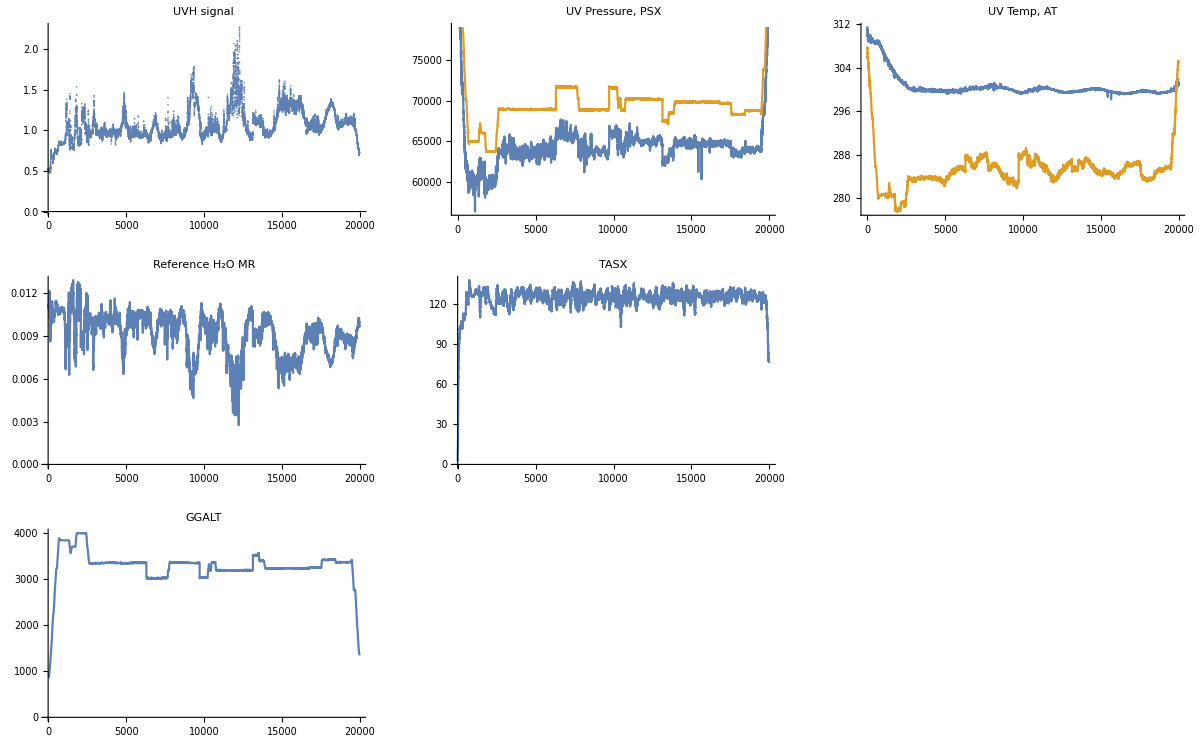

```mathematica
GraphicsGrid[{{ListPlot[oneHzDataMatrix[[All,iXSIGV]],PlotLabel->"UVH signal", PlotRange->All],
ListPlot[{oneHzDataMatrix[[All,iXCELLPRES]],oneHzDataMatrix[[ All,iPSX]]},PlotLabel->"UV Pressure, PSX",Joined->True],ListPlot[{oneHzDataMatrix[[All,iXCELLTEMP]],oneHzDataMatrix[[All, iAT]]},PlotLabel->"UV Temp, AT",Joined->True]},
{ListPlot[h2oReference[[All,2]], PlotLabel->"Reference H_2O MR", Joined->True,Joined->True],
ListPlot[oneHzDataMatrix[[All,iTASX]],PlotLabel->"TASX",Joined->True,PlotRange->All]},
{ListPlot[oneHzDataMatrix[[All,iGGALT]],PlotLabel->"GGALT",Joined->True,PlotRange->All]}},ImageSize->Full]
```

## Calculate number density in cell

Find H2O number density (m^-3) in the sample cell from the reference water  vapor mixing ratio, adjusting for the conditions in the sample cell.

```mathematica
densityCell=h2oReference[[All,h2oMR]]*oneHzDataMatrix[[All,iXCELLPRES]]/(oneHzDataMatrix[[All,iXCELLTEMP]]*kB);

(* SomethingPlot variables are created for convenience in plotting data. Consists of {time,value}. *)
densityCellPlot=Transpose[{oneHzDataMatrix[[All,iTIME]], densityCell}];
```

## Adjust signal voltage for window and O2 absorption

```mathematica
(* Adjust xsigv for lamp decay & window contamination.
LinearDecayRate (set in Initialization) determined by trial and error.
LinearDecayStartTime is the first time in the trimmed files. It's needed because the output calculations may have a different start time. *)
linearDecayStartTime=oneHzDataMatrix[[1,iTIME]]

(* Temporary variable *)
temp=Table[oneHzDataMatrix[[i,iXSIGV]]+linearDecayRate*i,{i,1,Length[oneHzDataMatrix]}];

(* Atmospheric oxygen also absorbs the UV light, so adjust xsigv for cell pressure using simple Beer's law. The value (-0.25E-5 V/Pascal) was determined by trial and error. *)
xsigvAdj=temp/Exp[-0.25*oneHzDataMatrix[[All,iXCELLPRES]]*10^-5];
```

68756

## Fit number density to signal voltage

```mathematica
(* Create data array for fit. Factor out 10^22 in molecular density so values are near unity. *)
fitArray=Transpose[{10^-22*densityCell,xsigvAdj}];

(* Remove the first 'dropAtStart' points which never fit well. *)
fitArray=Drop[fitArray,dropAtStart];
Length[fitArray]

(* Calculate least-squares fit. I've modified some of these by hand (see below) because the fit is biased by some portions. Also there is substantial correlations between the variables such that they can differ greatly from the rest of the flights so I'll manually adjust them so that the values are similar between different flights. *)
fit=FindFit[fitArray,model,{{a,0},{b,5},{σl,0.2}},x]
```

17978

{a→-0.404733,b→3.14983,σl→0.0453735}

```mathematica
(* Hand-tuned values to use in generating output. See above comments. *)
fit={a->0.43,b->3.28,σl->0.0989};
```

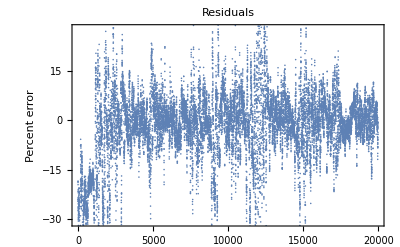

```mathematica
ListPlot[100*(densityCell-densityEqn[xsigvAdj]/.fit)/densityCell, Frame->True,FrameLabel->{"","Percent error"}, PlotLabel->"Residuals", ImageSize->Scaled[0.8]]
```

## Invert for number density from Voltage

Reread the .nc file for time and uvh values to calculate mixing ratio without any gaps.

```mathematica
calcDataMatrix=Transpose[{Import[datafile,{"Datasets","Time"}],Import[datafile,{"Datasets","XSIGV_UVH"}],Import[datafile,{"Datasets","XCELLPRES_UVH"}]*100,Import[datafile,{"Datasets","XCELLTEMP_UVH"}]+273.15}];
```

```mathematica
(* Drop drop from calcDataMatrix if it starts earlier than the h2oReference. *)
If [h2oReference[[1,1]]> calcDataMatrix[[1,1]],{"Dropping data at start",calcDataMatrix=Drop[calcDataMatrix,h2oReference[[1,1]]-calcDataMatrix[[1,1]]]}]
```

{Dropping data at start,{{68809,0.49844,82711.8,309.114},{68810,0.499175,82864.6,309.164},21189,{90000,-0.0111426,11589.9,352.411}}}
 |  |  |  |

```mathematica
(* Ditto for end of data. *)
If [h2oReference[[-1,1]]< calcDataMatrix[[-1,1]],{"Dropping lines at end",calcDataMatrix=Drop[calcDataMatrix,h2oReference[[-1,1]]-calcDataMatrix[[-1,1]]]}]
```

{Dropping lines at end,{{68809,0.49844,82711.8,309.114},{68810,0.499175,82864.6,309.164},20878,{89689,0.687098,86212.6,301.742}}}
 |  |  |  |

```mathematica
(* Adjust xsigv for lamp decay & window contamination. *)
temp=Table[calcDataMatrix[[i,2]]+linearDecayRate*(calcDataMatrix[[i,1]]-linearDecayStartTime),{i,1,Length[calcDataMatrix]}];

(* Adjust xsigv for pressure (O2 adsorption). *)
calcXsigvAdj=temp/Exp[-0.25*calcDataMatrix[[All,3]]*10^-5];
```

```mathematica
(* Calculate H2O number density in the UVH cell. *)densityCalc=densityEqn[calcXsigvAdj]/.fit;
densityCalcPlot=Transpose[{calcDataMatrix[[All,1]],densityCalc}];
```

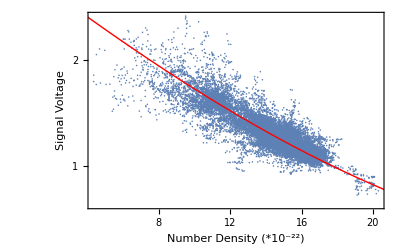

```mathematica
GraphicsColumn[{ListPlot[{densityCellPlot,densityCalcPlot},PlotStyle->{Red,Blue},Frame->True],
Show[ListLogPlot[fitArray,Frame->True,FrameLabel->{"Number Density (*10^-22)","Signal Voltage"},PlotRange->All],LogPlot[a+b Exp[-σl x]/.fit,{x,0.2,40},PlotStyle->{Red,Thick}]]},ImageSize->Scaled[0.8]]
```

## Convert Number Density to Mixing Ratio (ppmv)

Calculate mixing ratio present in the sample cell.

```mathematica
(* Need total gas density in the cell. *)calcCellDensity=calcDataMatrix[[All,3]]/(calcDataMatrix[[All,4]]*kB);
mr=densityCalc/calcCellDensity; (* NOT yet in ppm here! *)
mrPlot=Transpose[{calcDataMatrix[[All,1]],mr}];
Dimensions[mr]
```

{20881}

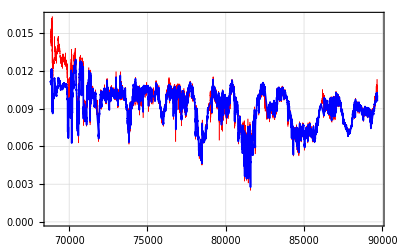

```mathematica
ListPlot[{mrPlot,h2oReference},PlotRange->Automatic, ImageSize->Full, Joined->{True,True}, Frame->True, GridLines->Automatic, PlotStyle->{{Red,Thickness[0.001]},{Blue,Thickness[0.003]}}]
```

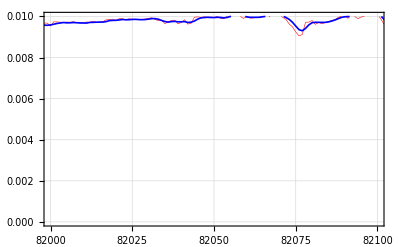

```mathematica
ListPlot[{mrPlot,h2oReference},PlotRange->{{82000,82100},{0.00,.01}}, ImageSize->Full, Joined->{True,True}, Frame->True, GridLines->Automatic, PlotStyle->{{Red,Thickness[0.001]},{Blue,Thickness[0.003]}}]
```

## Export data as ascii values of mixing ratio

Export time to two digits past decimal point. Multiply mixing ratio by 10^6 to get ppmv and export to at least 4 digits.

```mathematica
exportData=Transpose[{mrPlot[[All,1]],mrPlot[[All,2]]*1000000.0}];
```

```mathematica
Export[exportFile, NumberForm[exportData,{6,1}],"Table"]
```